# SR1 and SMW

The SMW identity gives a cheap way to solve a slightly modified linear system.  The SR1 update formula is a simple way to incorporate a “secant” piece of information into an approximation to a symmetric matrix. We are going to look at both these “little” pieces of linear algebra alone and then incorporate them into a simple optimization algorithm.

### Sherman Morrison Woodbury (SMW)

The lemma says that
	(A+U.C.V)^-1=A^-1-A^-1.U.(C^-1+V.A^-1.U)^-1.V.A^-1
Checking this analytically or numerically is easy.  I am doing numerically basically just to check I have not mistyped anything. It looks like it works.

```mathematica
{m,r}={12,3};
A=RandomReal[{-1,1},{m,m}];
CMat=RandomReal[{-1,1},{r,r}];
U=RandomReal[{-1,1},{m,r}];
V=RandomReal[{-1,1},{r,m}];
InvA=Inverse[A];
SMW=InvA-InvA.U.Inverse[Inverse[CMat]+V.InvA.U].V.InvA;
Norm[Inverse[A+U.CMat.V]-SMW]
```

1.2685×10^-14

So what is it good for?  It is useful if we know some way to compute A^-1 or maybe A^-1.y cheaply and we want to solve (A+U.C.V)z=b.  Quasi-Newton algorithms choose updates to make this useful.

The simplest version (called the Sherman Morrison lemma) is when U is the ultimate tall skinny matrix (a single column) and V is the ultimate short stout matrix (a single row). This gives an expression for the inverse of A+u⊗v. This is the version underlying the standard (non-block) QN optimization algorithms.  Here is a function implementing it.

```mathematica
SM[A_,{u_,v_}]:= Module[{InvA=Inverse[A]},

InvA-InvA.(KroneckerProduct[u,v]/(1+v.InvA.u)).InvA
]
(* Testing *)
m=12;
A=RandomReal[{-1,1},{m,m}];
{u,v}=RandomReal[{-1,1},{2,m}];
Inverse[A+KroneckerProduct[u,v]]-SM[A,{u,v}]
```

{{-1.66533×10^-15,7.88258×10^-15,8.88178×10^-16,-1.33227×10^-15,1.9984×10^-15,-1.9984×10^-15,7.77156×10^-16,-6.66134×10^-15,3.9968×10^-15,-4.996×10^-16,3.21965×10^-15,1.22125×10^-15},{-5.55112×10^-17,-3.33067×10^-16,8.32667×10^-17,2.08167×10^-16,5.55112×10^-17,5.20417×10^-16,2.98372×10^-16,3.67328×10^-16,1.94289×10^-16,1.11022×10^-16,-8.32667×10^-16,-6.93889×10^-17},{6.10623×10^-15,5.55112×10^-15,1.88738×10^-15,-1.14492×10^-15,5.10703×10^-15,-7.32747×10^-15,-2.83107×10^-15,-7.32747×10^-15,5.10703×10^-15,-7.21645×10^-16,3.21965×10^-15,5.55112×10^-16},{0.,-3.88578×10^-16,-2.22045×10^-16,-1.11022×10^-16,-4.996×10^-16,6.10623×10^-16,1.11022×10^-16,1.66533×10^-16,0.,2.77556×10^-16,-1.11022×10^-16,-2.77556×10^-16},{-2.06779×10^-15,-6.4948×10^-15,-1.11022×10^-15,1.09635×10^-15,-2.88658×10^-15,5.10703×10^-15,2.80331×10^-15,3.77476×10^-15,-4.996×10^-15,7.77156×10^-16,-7.10543×10^-15,-1.22125×10^-15},{6.45317×10^-16,1.38778×10^-15,3.33067×10^-16,-4.71845×10^-16,9.4369×10^-16,-9.4369×10^-16,-1.66533×10^-16,-1.22125×10^-15,1.33227×10^-15,-5.55112×10^-17,1.33227×10^-15,1.11022×10^-16},{-3.33067×10^-16,4.44089×10^-16,2.22045×10^-16,0.,5.55112×10^-17,-2.22045×10^-16,1.11022×10^-16,-5.55112×10^-16,4.44089×10^-16,0.,2.498×10^-16,4.996×10^-16},{3.33067×10^-16,1.11022×10^-15,3.05311×10^-16,-3.60822×10^-16,4.64906×10^-16,-4.71845×10^-16,-8.32667×10^-16,-1.07553×10^-15,1.55431×10^-15,-2.77556×10^-16,8.8124×10^-16,3.33067×10^-16},{1.1241×10^-15,3.71925×10^-15,1.55431×10^-15,-8.32667×10^-16,1.77636×10^-15,-3.55271×10^-15,-1.05471×10^-15,-2.66454×10^-15,2.2482×10^-15,-1.94289×10^-16,2.30371×10^-15,9.99201×10^-16},{-1.11022×10^-16,1.66533×10^-16,-2.22045×10^-16,-2.22045×10^-16,2.22045×10^-16,3.33067×10^-16,-1.11022×10^-16,-8.32667×10^-17,1.11022×10^-16,-1.66533×10^-16,-2.42861×10^-17,8.32667×10^-17},{1.11022×10^-16,1.11022×10^-16,5.55112×10^-17,-2.22045×10^-16,3.33067×10^-16,-1.11022×10^-16,-1.66533×10^-16,-3.05311×10^-16,5.55112×10^-17,5.55112×10^-17,1.11022×10^-16,-5.55112×10^-17},{-3.33067×10^-16,1.88738×10^-15,5.55112×10^-16,0.,8.88178×10^-16,-9.4369×10^-16,-2.77556×10^-16,-8.88178×10^-16,1.11022×10^-16,-3.50414×10^-16,1.17614×10^-15,7.25114×10^-16}}

### SR1 Updates

The simplest symmetric update of a symmetric matrix B_k to a matrix B_(k+1) satisfying the secant condition
	B_(k+1)s=y
is the SR1 update
	 B_(k+1)=B_k+((y-B_k.s)⊗(y-B_k.s))/((y-B_k.s).s)
it is well defined provided (y-B_k.s).s≠0.  Again it is easy to check analytically or numerically that it works. The following is going to verify that random samples can drive approximations to a given symmetric matrix. First just making an update function and testing that it does what we think it should!

```mathematica
SR1[Bk_,{s_,y_}]:=Module[{z=y-Bk.s,α,Tol=1.0*10^-10},
α=z.s;
If[Abs[α]>Tol, Bk+KroneckerProduct[z,z]/α,Bk]
]
```

```mathematica
(* testing *)
m=12;
{B,Bk}=RandomReal[{-1,1},{2,m,m}];
{B,Bk}={B,Bk}+{Bᵀ,Bkᵀ};
s=RandomReal[{-1,1},m];
y=B.s;
BNew=SR1[Bk,{s,y}];
Norm[y-BNew.s]
```

7.79848×10^-15

This looks good. I am going to pick random directions and correct in those directions to see what happens.  In some sense this should not be surprising! If I correct in enough “independent” directions I will have “hit” all the directions there are!

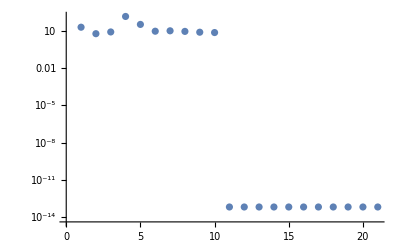

```mathematica
m=11;
{B,Bk}=RandomReal[{-1,1},{2,m,m}];
{B,Bk}={B,Bk}+{Bᵀ,Bkᵀ};
MaxIter=21;
Data=Table[
s=RandomReal[{-1,1},m];
y=B.s;
Bk=SR1[Bk,{s,y}];
Norm[B-Bk],
{MaxIter}
];
ListLogPlot[Data]
```